номер зачётки: 2022091

# Визуализация данных

## 1. Команды построения графиков. Примитивы и директивы двумерной графики.

## График с установками по умолчанию

```mathematica
Clear[f1, f2, f3, n];
n = 1;
f1[x_]:=Sin[x^2]
f2[x_]:=x+Sin[2 x^2.5]
f3[x_]:=x Sin[1.5 x^3]-x
```

```mathematica
Clear[f11, f22, f33, n];
n=1;
f11[x_]:=Sin[(x+n)^2]
f22[x_]:=x+Sin[2 (x+1/(n+1))^2.5]
f33[x_]:=x Sin[(n+1) x^3]-x
```

Задание 1

Записать команду Plot для построения графиков всех заданных выше функций на одном рисунке. Указать изменение переменной от -3 до +3.

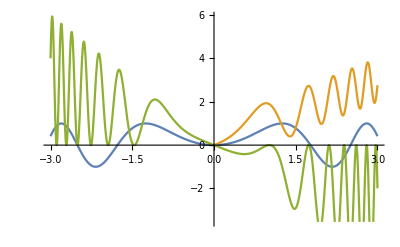

```mathematica
Plot[{f1[x], f2[x], f3[x]}, {x, -3, 3}]
```

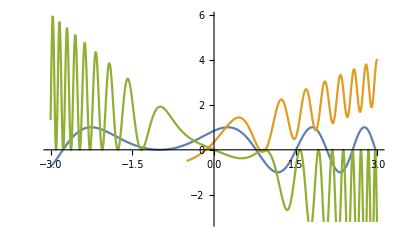

```mathematica
Plot[{f11[x], f22[x], f33[x]}, {x, -3, 3}]
```

## Вывод двух графических объектов в один ряд

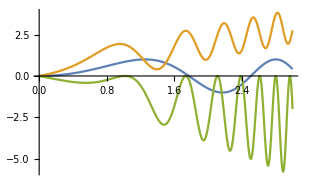
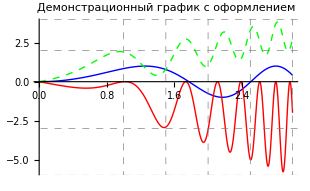

```mathematica
imageSize=310;
grf1=Plot[{f1[x],f2[x],f3[x]},{x,0,3}, ImageSize->imageSize];
grf2=Plot[{f1[x],f2[x],f3[x]},{x,0,3}, ImageSize->imageSize, PlotStyle->{{Blue,Thin},{Green,Thick,Dashed},{Red,Thick}},AxesStyle->{Directive[Black,Thick,14],Directive[Blue,Thick,14]},GridLines->{{1,1.5,2,2.5,3},{-6,-3,2,4}},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->Style[Framed["Демонстрационный график с оформлением",FrameStyle->Red,RoundingRadius->5],12,Plain,Blue,Background->LightYellow]];
{grf1,grf2}
```

Задание 2

1. Исправьте в приведенном выше коде команды так, чтобы рисунки выводились на экран. 

2. Опишите назначение: 
ImageSize, 

PlotStyle→{{Blue,Thin},{Green,Thick,Dashed},{Red,Thick}},

AxesStyle→{Directrix[Black,Thick,14],Directive[Blue,Thick,14]},

GridLines→{{1,1.5,2,2.5,3},{-6,-3,2,4}},

GridLinesStyle→Directive[Gray, Dashed],

PlotLabel→Style[Framed[“демографик с оформлением”,FrameStyle→Red,RoundingRadius→5],12,Plain,Blue,Background→LightYellow]]

Указать изменение переменной  -3 до +3 и выполнить построение заново.

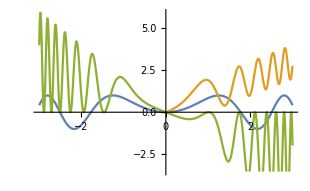
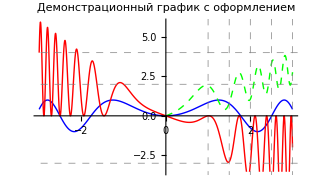

```mathematica
imageSize=310;
grf1=Plot[{f1[x],f2[x],f3[x]},{x,-3,3}, ImageSize->imageSize];
grf2=Plot[{f1[x],f2[x],f3[x]},{x,-3,3}, ImageSize->imageSize, PlotStyle->{{Blue,Thin},{Green,Thick,Dashed},{Red,Thick}},AxesStyle->{Directive[Black,Thick,14],Directive[Blue,Thick,14]},GridLines->{{1,1.5,2,2.5,3},{-6,-3,2,4}},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->Style[Framed["Демонстрационный график с оформлением",FrameStyle->Red,RoundingRadius->5],12,Plain,Blue,Background->LightYellow]];
{grf1,grf2}
```

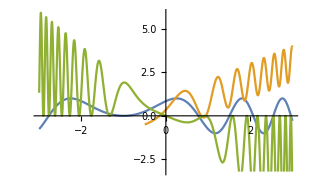
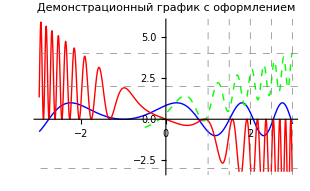

```mathematica
imageSize=310;
grf1=Plot[{f11[x],f22[x],f33[x]},{x,-3,3}, ImageSize->imageSize];
grf2=Plot[{f11[x],f22[x],f33[x]},{x,-3,3}, ImageSize->imageSize, PlotStyle->{{Blue,Thin},{Green,Thick,Dashed},{Red,Thick}},AxesStyle->{Directive[Black,Thick,14],Directive[Blue,Thick,14]},GridLines->{{1,1.5,2,2.5,3},{-6,-3,2,4}},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->Style[Framed["Демонстрационный график с оформлением",FrameStyle->Red,RoundingRadius->5],12,Plain,Blue,Background->LightYellow]];
{grf1,grf2}
```

imageSize - это параметр, определяющий общий размер изображения, отображаемого для объекта.
PlotStyle->{{Blue,Thin},{Green,Thick,Dashed},{Red,Thick}} - набор стилевых свойств, определяющий цвет, толщину линий и вид линии графиков.
В данном случае первый график отображается синей тонкой линией, второй - зеленой толстой пунктирной линией, третий - красной толстой линией.
AxesStyle->{Directrix[Black,Thick,14],Directive[Blue,Thick,14]}, - это свойство стилизирует координатные оси. Directix(ve) задает стили направляющим. Первый Directive отвечает за ось Ox, а второй Directive за Oy. В данном случае  ось Ox отображается черной толстой линией и таким же текстом с размером шрифта 14, ось Oy отображается синей толстой линией 14 размером шрифта.
GridLines->{{1,1.5,2,2.5,3},{-6,-3,2,4}} - определяет линии сетки. Первый список задает координаты вертикальных прямых сетки по х, второй - координаты горизонтальных прямых сетки по у.
GridLinesStyle->Directive[Gray, Dashed] - задает стили линиям сетки. В данном случае они отображаются серыми пунктирными линиями.
PlotLabel->Style[Framed[“демографик с оформлением”,FrameStyle->Red,RoundingRadius->5],12,Plain,Blue,Background->LightYellow]].
PlotLabel - определяет заголовок графика. Далее определяются стили заголовка графика. Framed - создает рамку. Первый параметр команды Framed - текст заголовка, FrameStyle - цвет рамки (красный). RoundingRadius - радиус закругления углов(5)
12,Plain,Blue,Background→LightYellow - 12-ый размер шрифта, Plain - обычный тип шрифта, цвет текста синий, цвет фона желтый

Задача 1

Построить совместные графики функций f(x)=5 x^4-12 x^3+8 x^2+2  и её производной на интервале (-1+n, 2+1/(n+1)). Сравните интервалы убывания и возрастания функции со знаком производной.
Измените цвет графика функции на зеленый, а производной на синий.

Решение:

```mathematica
D[5 x^4-12 x^3+8 x^2+2,x]
```

16 x-36 x^2+20 x^3

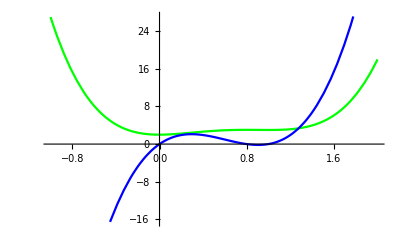

```mathematica
Plot[
{5 x^4-12 x^3+8 x^2+2,
16 x-36 x^2+20 x^3},
{x,-1,2},PlotStyle->{RGBColor[0,255,0],RGBColor[0,0,255]}]
```

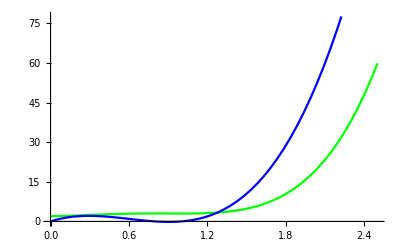

```mathematica
n = 1;
Plot[
{5 x^4-12 x^3+8 x^2+2,
16 x-36 x^2+20 x^3},
{x,-1+n,2+1/(n+1)},PlotStyle->{RGBColor[0,255,0],RGBColor[0,0,255]}]
```

## 2. Трехмерная графика.

Задача 2

Дана функция f(x,y)=xy+z. Подсчитать градиент этой функции.

Решение:

```mathematica
Grad[f[x,y,z],{x,y,z}]
```

{f^(1,0,0)[x,y,z],f^(0,1,0)[x,y,z],f^(0,0,1)[x,y,z]}

```mathematica
Grad[x y+z,{x,y,z}]
```

{y,x,1}

```mathematica
VectorPlot3D[{x, y, z}, {x, 0, 1}, {y, 0, 1}, {z, 0, 1}]
```

-Graphics3D-

```mathematica
VectorFieldPlot3D[{y,x,1},{x,-1,1},{y,-1,1},{z,1,1.5},PlotPoints->3]
```

-Graphics3D-

```mathematica
VectorFieldPlot3D[{y,x,1},{x,-1,1},{y,-1,1},{z,1,3},PlotPoints->5,VectorHeads->True]
```

-Graphics3D-

```mathematica
GradientFieldPlot3D[x y+z,{x,-1,1},{y,-1,1},{z,1,3},PlotPoints->10,VectorHeads->True]
```

-Graphics3D-

Ещё пример векторного поля

```mathematica
VectorFieldPlot3D[{y,-x,0}/z,{x,-1,1},{y,-1,1},{z,1,3},PlotPoints->10,VectorHeads->False]
```

-Graphics3D-

Поле градиентов для функции f(x,y,z)=x y z

```mathematica
GradientFieldPlot3D[x y z,{x,-1,1},{y,-1,1},{z,-1,1},PlotPoints->10,VectorHeads->True]
```

Задание 3

Кликните правой кнопкой мыши по построенному графику. В меню проверьте работу всех пунктов, которые отвечают за просмотр.

Front View - вид спереди
Top View - вид сверху
Default View - стандартный вид
Reset Pan/Zoom - сбрасывает панораму и масштаб выбранной трехмерной графики.

Задача 3

Дано векторное поле v в трехмерном пространстве v={ f (x,y,z),g(x,y,z),h(x,y,z)}. Получить выражение для дивергенции этого векторного поля.

Решение:

```mathematica
Div[{x ,x y,x y z},{x,y,z}]
```

1+x+x y

```mathematica
gr1=Plot3D[
Div[{x ,x y,x y z},{x,y,z}]//Evaluate,
{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
gr2=VectorFieldPlot3D[{x ,x y,x y z},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,VectorHeads->True]
```

-Graphics3D-

```mathematica
Show[gr2,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Show[gr2,ViewPoint->{0,∞,0}]
```

-Graphics3D-

```mathematica
Show[gr1,gr2]
```

-Graphics3D-

Задание

Выяснить, можно ли изменить в опциях длину штрихов и величину стрелочек?
Попробуйте сделать это.

За длину штрихов и, соответственно, стрелочек отвечает опция ScaleFactor→

```mathematica
GradientFieldPlot3D[x y z,{x,-1,1},{y,-1,1},{z,-1,1},PlotPoints->3,VectorHeads->True,ScaleFactor->5]
```

-Graphics3D-